```mathematica
SpinMatrix[k1_,k2_,a_,ϵ1_,ϵ2_,t0_,t1_,t2_,t11_,t12_,t22_,λ_]:={{ϵ1+2*t0*(Cos[a*k1]+2*Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]),-2*Sqrt[3]*t2*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]+2*I*t1*(Sin[a*k1]+Sin[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]),2*t2*(Cos[a*k1]-Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)])+2*Sqrt[3]*I*t1*Cos[a*k1/2]*Sin[a*k2*(Sqrt[3]/2)],0,0,0},{-2*Sqrt[3]*t2*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]-2*I*t1*(Sin[a*k1]+Sin[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]),ϵ2+2*t11*Cos[a*k1]+(t11+3*t22)*Cos[a*k1/2]*Cos[a*k2*(Sqrt[3]/2)],Sqrt[3]*(t22-t11)*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]+4*I*t12*Sin[a*k1/2]*(Cos[a*k1/2]-Cos[a*k2*(Sqrt[3]/2)])+λ*I,0,0,0},{2*t2(Cos[a*k1]-Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)])-2*Sqrt[3]*I*t1*Cos[a*k1/2]*Sin[a*k2*(Sqrt[3]/2)],Sqrt[3]*(t22-t11)*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]-4*I*t12*Sin[a*k1/2]*(Cos[a*k1/2]-Cos[a*k2*(Sqrt[3]/2)])-λ*I,ϵ2+2*t22*Cos[a*k1]+(3*t11+t22)*Cos[a*k1/2]*Cos[a*k2*(Sqrt[3]/2)],0,0,0},{0,0,0,ϵ1+2*t0*(Cos[a*k1]+2*Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]),-2*Sqrt[3]*t2*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]+2*I*t1*(Sin[a*k1]+Sin[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]),2*t2*(Cos[a*k1]-Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)])+2*Sqrt[3]*I*t1*Cos[a*k1/2]*Sin[a*k2*(Sqrt[3]/2)]},{0,0,0,-2*Sqrt[3]*t2*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]-2*I*t1*(Sin[a*k1]+Sin[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]), ϵ2+2*t11*Cos[a*k1]+(t11+3*t22)*Cos[a*k1/2]*Cos[a*k2*(Sqrt[3]/2)],Sqrt[3]*(t22-t11)*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]+4*I*t12*Sin[a*k1/2]*(Cos[a*k1/2]-Cos[a*k2*(Sqrt[3]/2)])-λ*I},{0,0,0,2*t2(Cos[a*k1]-Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)])-2*Sqrt[3]*I*t1*Cos[a*k1/2]*Sin[a*k2*(Sqrt[3]/2)],Sqrt[3]*(t22-t11)*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]-4*I*t12*Sin[a*k1/2]*(Cos[a*k1/2]-Cos[a*k2*(Sqrt[3]/2)])+λ*I,ϵ2+2*t22*Cos[a*k1]+(3*t11+t22)*Cos[a*k1/2]*Cos[a*k2*(Sqrt[3]/2)]}};

MasterHamiltonian[k1_,k2_,a_,ϵ1_,ϵ2_,t0_,t1_,t2_,t11_,t12_,t22_]:={{ϵ1+2*t0*(Cos[a*k1]+2*Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]),-2*Sqrt[3]*t2*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]+2*I*t1*(Sin[a*k1]+Sin[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]),2*t2*(Cos[a*k1]-Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)])+2*Sqrt[3]*I*t1*Cos[a*k1/2]*Sin[a*k2*(Sqrt[3]/2)]},{-2*Sqrt[3]*t2*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]-2*I*t1*(Sin[a*k1]+Sin[a*k1/2]Cos[a*k2*(Sqrt[3]/2)]), ϵ2+2*t11*Cos[a*k1]+(t11+3*t22)*Cos[a*k1/2]*Cos[a*k2*(Sqrt[3]/2)], Sqrt[3]*(t22-t11)*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]+4*I*0.338*Sin[a*k1/2]*(Cos[a*k1/2]-Cos[a*k2*(Sqrt[3]/2)])},{2*t2(Cos[a*k1]-Cos[a*k1/2]Cos[a*k2*(Sqrt[3]/2)])-2*Sqrt[3]*I*t1*Cos[a*k1/2]*Sin[a*k2*(Sqrt[3]/2)], Sqrt[3]*(t22-t11)*Sin[a*k1/2]Sin[a*k2*(Sqrt[3]/2)]-4*I*t12*Sin[a*k1/2]*(Cos[a*k1/2]-Cos[a*k2*(Sqrt[3]/2)]), ϵ2+2*t22*Cos[a*k1]+(3*t11+t22)*Cos[a*k1/2]*Cos[a*k2*(Sqrt[3]/2)]}};
a=.316;
(*a is the interatomic spacing, 3.16  Angstroms is its actual value*)
R=4*Pi/(3a);
f=Interpolation[Table[{a,R {Cos[a],Sin[a]}},{a,-Pi/2-2*π,Pi/2+2*π,π/3}],InterpolationOrder->1];
```

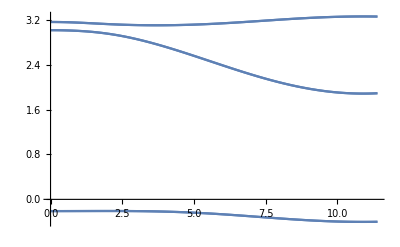

```mathematica
(*Band diagram plotted over the line where kx=0, ky runs from -R to R*)
p1=Plot[Sort[Re[Eigenvalues[SpinMatrix[0,ky,0.3326,0.919,2.065,-0.188,0.317,0.456,0.211,0.290,0.130,0.073]]]],{ky,0,11.4}]
```

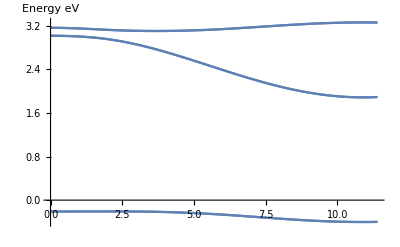

```mathematica
Show[p1,AxesLabel->{None,HoldForm[Energy eV]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

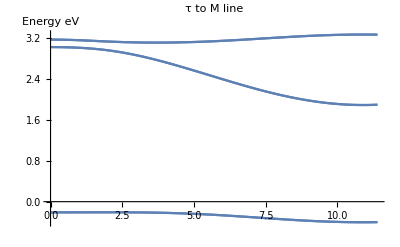

```mathematica
Show[%19,PlotLabel->HoldForm[τ to M line]]
```

```mathematica
Show[p1,AxesLabel->{None,HoldForm[Energy eV]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

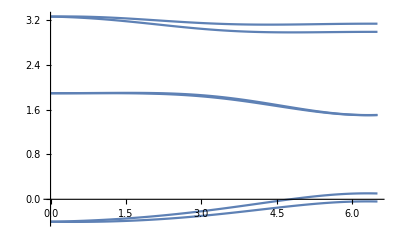

```mathematica
(*Band diagram plotted over the top boundary of the hexagon*)
p2=Plot[Sort[Re[Eigenvalues[SpinMatrix[kx,11.4,0.3326,0.919,2.065,-0.188,0.317,0.456,0.211,0.290,0.130,0.073]]]],{kx,0,6.5}]
```

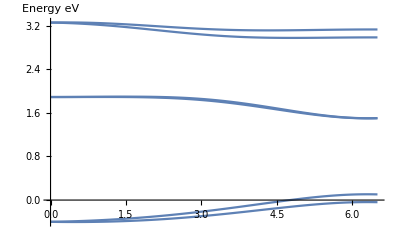

```mathematica
Show[p2,AxesLabel->{None,HoldForm[Energy eV]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

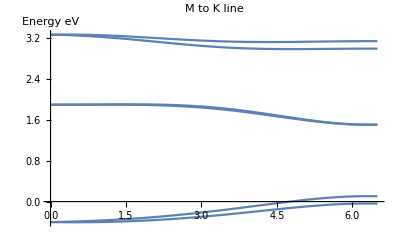

```mathematica
Show[%13,PlotLabel->HoldForm[M to K line]]
```

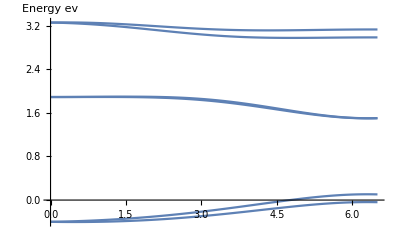

```mathematica
Show[p2,AxesLabel->{None,HoldForm[Energy ev]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

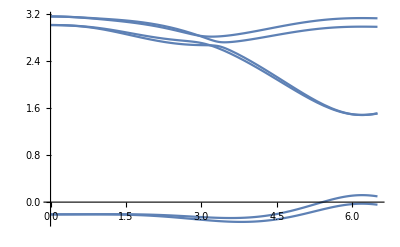

```mathematica
(*Band diagram plotted over the line running from the center of the hexagon out to the top right hand corner*)
p3=Plot[Sort[Re[Eigenvalues[SpinMatrix[kx,1.77kx,0.3326,0.919,2.065,-0.188,0.317,0.456,0.211,0.290,0.130,0.073]]]],{kx,0,6.5}]
```

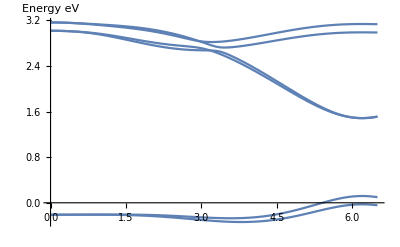

```mathematica
Show[p3,AxesLabel->{None,HoldForm[Energy eV]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

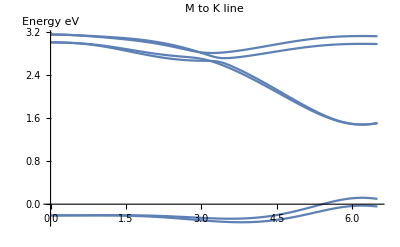

```mathematica
Show[%22,PlotLabel->HoldForm[M to K line]]
```

```mathematica
GraphicsRow[{p1,p2,p5}]
(*Plots in order are Γ->M->K->Γ*)
```

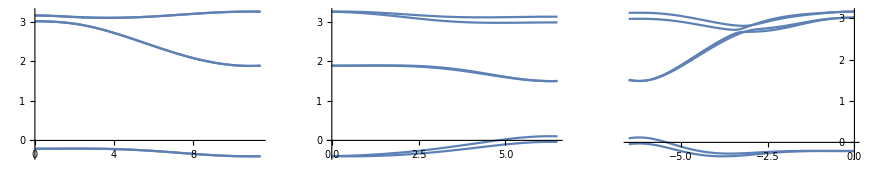

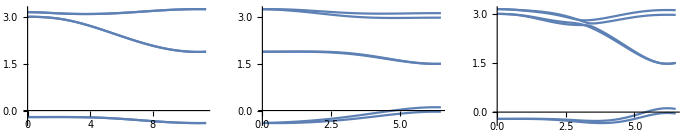

```mathematica
GraphicsRow[{p1,p2,p3}]
(*Plots are in the order Γ->M->K and then Γ->K*)
```

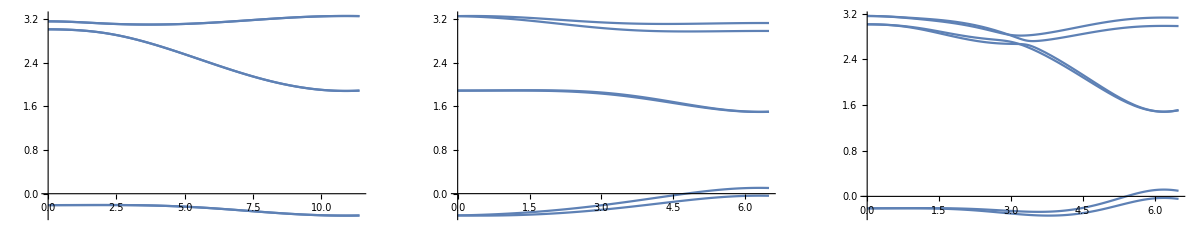

```mathematica
Show[%17,PlotLabel->HoldForm[Energy in eV plotted along symmetry points],LabelStyle->{FontFamily->"Al Bayan",GrayLevel[0]}]
```